## Brown/John T. Armstrong ϕ[ρz] algorithm

```mathematica
ϕ[ρz_]=γ0 Exp[-α^2 ρz^2] (1-q Exp[-β ρz])
```

ⅇ^(-α^2 ρz^2) (1-ⅇ^(-β ρz) q) γ0

Emitted x - ray intensity

```mathematica
Integrate[ϕ[ρz] Exp[-μ ρz / Sin[θ]],{ρz,0,∞},Assumptions->{ α>0, β>0}]
```

(√π γ0 (ⅇ^((μ^2 Csc[θ]^2)/(4 α^2)) Erfc[(μ Csc[θ])/(2 α)]-ⅇ^((β+μ Csc[θ])^2/(4 α^2)) q Erfc[(β+μ Csc[θ])/(2 α)]))/(2 α)

Generated x - ray intensity

```mathematica
Integrate[ϕ[ρz] ,{ρz,0,∞},Assumptions->{ α>0, β>0}]
```

-(√π γ0 (-1+ⅇ^(β^2/(4 α^2)) q Erfc[β/(2 α)]))/(2 α)

18 - Jun - 2008  NWMR

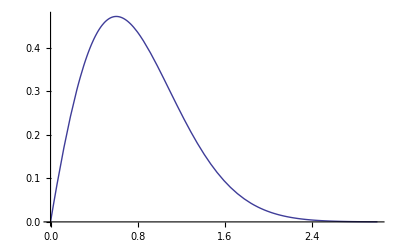

```mathematica
Plot[ϕ[ρz]/.{α->1,β->1,γ0->1.5,q->1},{ρz,0,3}]
```

```mathematica
ϕ[0.5]/.{α->1,β->1,γ0->1.5,q->1}
```

0.459651

```mathematica
Integrate[ϕ[ρz] ,{ρz,0,∞},Assumptions->{ α>0, β>0}]/.{α->1,β->1,γ0->1.5,q->1}
```

0.510878

```mathematica
Integrate[ϕ[ρz] Exp[-μ ρz / Sin[θ]],{ρz,0,∞},Assumptions->{ α>0, β>0}]/.{α->1,β->1,γ0->1.5,q->1,θ->0.7, μ->1}
```

0.179512

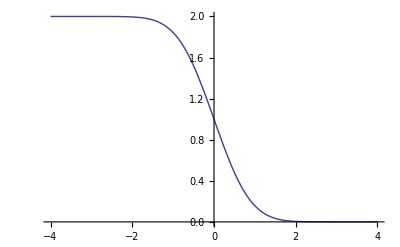

```mathematica
Plot[Erfc[x],{x,-4,4}]
```

```mathematica
Table[Erfc[x],{x,-4,4,0.5}]
```

{2.,2.,1.99998,1.99959,1.99532,1.96611,1.8427,1.5205,1.,0.4795,0.157299,0.0338949,0.00467773,0.000406952,0.0000220905,7.43098×10^-7,1.54173×10^-8}